## Introduction to Mathematica

## Section. Why Mathematica?

## Section. Wolfram Language

## Section. Structure of Mathematica

### Section.Subsection. Design Mathematica

```mathematica
1
```

```mathematica
(3*3)+(4/2)
```

11

## Section. Notebooks

### Section.Subsection. Text processing

### Section.Subsection. Palettes

## Section. Expression in Mathematica

```mathematica
2
```

```mathematica
(3*3)+(4/2)
```

11

```mathematica
3
```

```mathematica
100^2 10
```

100000

```mathematica
4
```

```mathematica
2*1
```

2

```mathematica
5
```

```mathematica
1/2+√2
```

1/2+√2

```mathematica
N[1/2+√2]
```

1.91421

```mathematica
7
```

```mathematica
N[77/13,10]
```

5.923076923

```mathematica
8
```

```mathematica
4./2+2/13
```

2.15385

```mathematica
9
```

```mathematica
11/7;
Sqrt[4]
```

2

```mathematica
10
```

```mathematica
3*4; 100*100; 1/4;
```

### Section.Subsection. Assigning values

```mathematica
11
```

```mathematica
a=Pi
x=11
z+y
```

π

11

y+z

12

```mathematica
%12
In[12]
Out[12]
```

π

π

π

13

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
14
```

```mathematica
Module[
{l=1,k=2,h=3} ,
l+k+h*Sqrt[l+k]
]
```

3+3 √3

```mathematica
15
```

```mathematica
{l,k,h}
```

{l,k,h}

```mathematica
16
```

```mathematica
Clear[a,x,y]
```

```mathematica
17
```

```mathematica
Head[a]
```

Symbol

### Section.Subsection. Built in Functions

```mathematica
18
```

```mathematica
RandomInteger[]
```

1

```mathematica
19
```

```mathematica
Sin[90Degree]+Cos[0 Degree]
```

2

```mathematica
20
```

```mathematica
Power[2,2]
```

4

```mathematica
21
```

```mathematica
d=Power[2,2]
f=Sin[π]+Cos[π]
```

4

-1

```mathematica
22
```

```mathematica
Clear[d,f]
```

```mathematica
23
```

```mathematica
Options[RandomReal]
```

{WorkingPrecision→MachinePrecision}

```mathematica
24
```

```mathematica
RandomReal[{0,1},WorkingPrecision->MachinePrecision]
RandomReal[{0,1},WorkingPrecision->30]
```

0.958544

0.0575431573212742364334809775045

```mathematica
25
```

```mathematica
Options[Power]
```

{}

### 5.3Dates and Time

```mathematica
26
```

```mathematica
DateObject[]
```

Thu 1 Oct 2020 22:48:31GMT-5.

```mathematica
27
```

```mathematica
Tomorrow
```

Day: Fri 2 Oct 2020

```mathematica
28
```

```mathematica
DateObject[{2020,6,10}]
```

Day: Wed 10 Jun 2020

```mathematica
29
```

```mathematica
DateObject[Today,CalendarType->"Julian"]
DateObject[Today,CalendarType->"Jewish"]
```

Day: Thu 18 Sep 2020 (Juliancalendar)

Day: Yom Chamishi 13 Tishrei 5781 (Jewishcalendar)

```mathematica
30
```

```mathematica
DateObject[{2010,3,4},TimeZone->"America/Belize"]
```

Day: Thu 4 Mar 2010

```mathematica
31
```

```mathematica
Sunset[Here,Now]
Sunrise[Here,Yesterday]
```

Minute: Fri 2 Oct 2020 19:23GMT-5.

Minute: Wed 30 Sep 2020 07:27GMT-5.

```mathematica
32
```

```mathematica
TimeObject[]
```

22:48:43TimeObject[{22,48,43.3015225},Instant,None]

```mathematica
33
```

```mathematica
TimeZoneConvert[TimeObject[{17,00,00},TimeZone->"America/Cancun"],"America/Los_Angeles"]
```

15:00:00PDTTimeObject[{15,0,0.},Instant,America/Los_Angeles]

### Section.Subsection. Basic Plotting

```mathematica
34
```

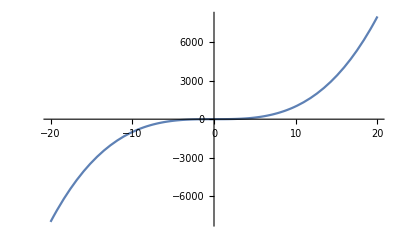

```mathematica
Plot[x^3,{x,-20,20}]
```

```mathematica
35
```

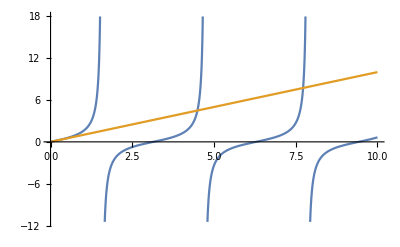

```mathematica
Plot[{Tan[x],x},{x,0,10}]
```

```mathematica
36
```

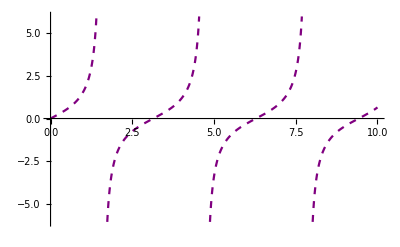

```mathematica
Plot[Tan[x],{x,0,10},PlotStyle->{Dashed,Purple}]
```

```mathematica
37
```

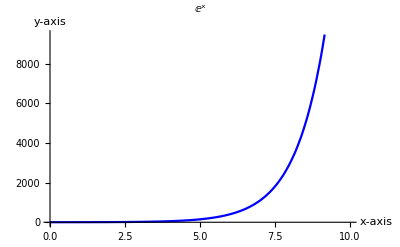

```mathematica
Plot[ⅇ^x,{x,0,10},PlotStyle->{Blue},PlotLabel->ⅇ^x,AxesLabel->{"x-axis","y-axis"}]
```

### Section.Subsection. Logical operators and Infix notation

```mathematica
38
```

```mathematica
6*1>2
```

True

```mathematica
39
```

```mathematica
6*1<2
```

False

```mathematica
40
```

```mathematica
1/2≥1/2
```

True

```mathematica
41
```

```mathematica
1/4≤1/2
```

True

```mathematica
42
```

```mathematica
3.12==2.72
```

False

```mathematica
43
```

```mathematica
π≠√-1
```

True

```mathematica
44
```

```mathematica
2==1&&3.12==2
```

False

```mathematica
45
```

```mathematica
2*2==3||23*2==1
```

False

```mathematica
46
```

```mathematica
2==1⊻ 2==2
```

True

```mathematica
47
```

```mathematica
Power[1,2]⧦ 1^2
```

True

True

```mathematica
48
```

```mathematica
¬2==1
```

True

```mathematica
49
```

```mathematica
IntegerQ[1]
IntegerQ[1.]
```

True

False

```mathematica
50
```

```mathematica
AtomQ[12]
```

True

### 5.6 Algebraic Expressions

```mathematica
51
```

```mathematica
Expand[((x^2)+y^2)*(x+y)]
```

x^3+x^2 y+x y^2+y^3

```mathematica
52
```

```mathematica
Expand[a x^2*(a x)^3]
```

a^4 x^5

```mathematica
53
```

```mathematica
Simplify[x^3+x^2 y+x y^2+y^3]
FullSimplify[x^3+x^2 y+x y^2+y^3]
```

x^3+x^2 y+x y^2+y^3

(x+y) (x^2+y^2)

```mathematica
54
```

```mathematica
Together[1/z+1/(z+1)-1/(z+2)]
Apart[(2+4 z+z^2)/(z (1+z) (2+z))]
```

(2+4 z+z^2)/(z (1+z) (2+z))

1/z+1/(1+z)-1/(2+z)

### 5.7 Solving algebraic equations

```mathematica
55
```

```mathematica
Solve[z^2+1==2,z]
```

{{z→-1},{z→1}}

```mathematica
56
```

```mathematica
z^2+1/.Rule[z, {1,-1}]
```

{2,2}

```mathematica
57
```

```mathematica
{1^2+1==2,(-1)^2+1==2}
```

{True,True}

```mathematica
58
```

```mathematica
Solve[{x+y+z==2,6x-4y+5z==3,x+2y+2z==1},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
59
```

```mathematica
EQ1=x+y+z==2;EQ2=6 x-4 y+5 z==3;EQ3=x+2 y+2 z==1;
Solve[{EQ1,EQ2,EQ3},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
60
```

```mathematica
Solve[{x+y+z==a,6x-4y+5z==b,x+2y+2z==c},{x,y,z}]
```

{{x→2 a-c,y→1/9 (7 a-b-c),z→1/9 (-16 a+b+10 c)}}

```mathematica
61
```

```mathematica
Solve[EQ1&&EQ2,{x,y}]
```

{{x→1/10 (11-9 z),y→(9-z)/10}}

```mathematica
62
```

```mathematica
Solve[x^2+y^2==0||x-2y==1,x]
```

{{x→-ⅈ y},{x→ⅈ y},{x→1+2 y}}

```mathematica
63
```

```mathematica
Solve[z^-2+1==2&&z!=1,z]
```

{{z→-1}}

```mathematica
64
```

```mathematica
Reduce[Cos[x]==-1,x]
```

C[1]∈ℤ&&(x==-π+2 π C[1]||x==π+2 π C[1])

```mathematica
65
```

```mathematica
Reduce[h^2+k^2<11,{h,k}]
```

-√11<h<√11&&-√(11-h^2)<k<√(11-h^2)

```mathematica
66
```

```mathematica
Reduce[α +β*α^2==E,α]
```

(β==0&&α==ⅇ)||(β≠0&&(α==(-1-√(1+4 ⅇ β))/(2 β)||α==(-1+√(1+4 ⅇ β))/(2 β)))

### 5.8 Using Wolfram Alpha inside Mathematica

```mathematica
67
```

Solve y^2 + x^2 == 1 && y + 2 x == 0, for {x, y}

WolframAlphaQueryResults

```mathematica
68
```

WolframAlphaQueryParseResults

(x==-1/(√5)||x==1/(√5))&&y==-2 x

```mathematica
69
```

WolframAlphaQueryResults

mean | $111.82  (US dollars)
highest | $149.90  (US dollars) (Wednesday, March 4, 2020)
lowest | $72.24  (US dollars) (Wednesday, March 18, 2020)
volatility | 146%
change | -30%

```mathematica
70
```

WolframAlphaQueryParseResults

25203200 people

### Section.Subsection. Delayed expressions

```mathematica
71
```

```mathematica
W=RandomReal[]
```

0.984947

72

```mathematica
W==W
```

True

73

```mathematica
Clear[W];W:=RandomReal[];W
```

0.931616

```mathematica
74
```

```mathematica
W==W
```

False

### 5.10 Code Performance

```mathematica
75
```

```mathematica
Timing[Power[10,100000000];]
```

{1.70313,Null}

```mathematica
76
```

```mathematica
Timing[10^100000000;]
```

{1.8125,Null}

```mathematica
77
```

```mathematica
AbsoluteTiming[10^100000000;]
```

{2.11773,Null}

```mathematica
78
```

```mathematica
AbsoluteTiming[Power[10,100000000];]
```

{2.68439,Null}

79

```mathematica
TimeConstrained[10^100000000,1]
```

$Aborted

### Section.Subsection. Strings

```mathematica
80
```

```mathematica
"Hello World" (* This is a comment*)
```

Hello World

81

```mathematica
ToString[23.423563]
```

23.4236

```mathematica
82
```

```mathematica
%//Head(* We use Head to knwo what type of objetc is *)
```

String

```mathematica
83
```

```mathematica
"Welcome to Mathematica"
```

Welcome to Mathematica

```mathematica
84
```

```mathematica
AtomQ["The sky is blue and tomorrow is expected to rain"]
```

True

85

```mathematica
Characters["Hello World"] (*Function that breaks the string into its characters*)
```

{H,e,l,l,o, ,W,o,r,l,d}

86

```mathematica
StringReplace["Hello this is a string ", {"h","H"}->"4"]
(*This function repalce the string each time it appears for rule of the pattern, that is 4*)
```

4ello t4is is a string

87

```mathematica
ToUpperCase["hello my name is"]
```

HELLO MY NAME IS

88

```mathematica
ToLowerCase["HELLO MY NAME IS"]
```

hello my name is

89

```mathematica
StringJoin["Nice","to","have","you","back"]
```

Nicetohaveyouback

90

```mathematica
"Nice"<>"to"<>"have"<>"you"<>"back"
```

Nicetohaveyouback

## Section. How Mathematica Works

### Section.Subsection. How computations are made (Form of Input)

```mathematica
91
```

```mathematica
StandardForm[1/x + x^2]
```

1/x+x^2

92

```mathematica
{InputForm[1/x+x^2],InputForm[a^x],InputForm[Subscript[a, x]],InputForm[√2]}
```

{x^(-1) + x^2,a^x,Subscript[a, x],Sqrt[2]}

93

```mathematica
FullForm[t/2+2^2]
```

Plus[4,Times[Rational[1,2],t]]

94

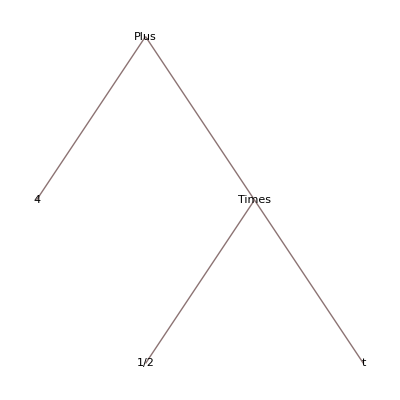

```mathematica
t/2+2^2//TreeForm
```

95

```mathematica
Trace[Plus[4,Times[Rational[1,2],t]]]
```

{{{Rational[1,2],1/2},t/2},4+t/2}

96

```mathematica
FullForm[Trace[Plus[4,Times[Rational[1,2],t]]]]
```

List[List[List[HoldForm[Rational[1,2]],HoldForm[Rational[1,2]]],HoldForm[Times[Rational[1,2],t]]],HoldForm[Plus[4,Times[Rational[1,2],t]]]]

97

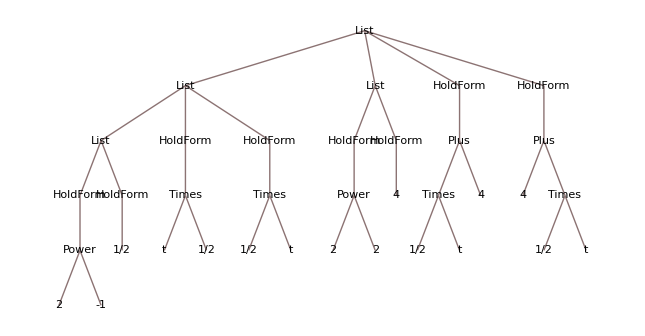

```mathematica
Trace[t/2+2^2]//TreeForm
```

### Section.Subsection. Searching for Assistance

```mathematica
98
```

```mathematica
?Head
```

```mathematica
99
```

```mathematica
?Hea*
```

### 6.3 Handling Errors

```mathematica
100
```

```mathematica
StringJoin["hello","I am ",Jeff]
```

StringJoin::string: String expected at position 2 in helloI am <>Jeff.

helloI am <>Jeff

```mathematica
101
```

```mathematica
Power[x/0,2]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

### 6.4 Notebook Security

```mathematica
102
```

```mathematica
$BaseDirectory
```

C:\ProgramData\Mathematica

```mathematica
103
```

```mathematica
$UserBaseDirectory
```

C:\Users\lb-pc\AppData\Roaming\Mathematica

```mathematica
104
```

```mathematica
$InitialDirectory
```

C:\Users\lb-pc\Documents